Expressions and Their Structure

We’ve now seen all sorts of things that exist in the Wolfram Language: lists, graphics, pure functions and much more. And now we’re ready to discuss a very fundamental fact about the Wolfram Language: that each of these things—and in fact everything the language deals with—is ultimately constructed in the same basic kind of way. Everything is what’s called a symbolic expression.

Symbolic expressions are a very general way to represent structure, potentially with meaning associated with that structure. f[x,y] is a simple example of a symbolic expression. On its own, this symbolic expression doesn’t have any particular meaning attached, and if you type it into the Wolfram Language, it’ll just come back unchanged.

f[x,y] is a symbolic expression with no particular meaning attached:

```mathematica
f[x,y]
```

f[x,y]

{x,y,z} is another symbolic expression. Internally, it’s List[x,y,z], but it’s displayed as {x,y,z}.

The symbolic expression List[x,y,z] displays as {x,y,z}:

```mathematica
List[x,y,z]
```

{x,y,z}

Symbolic expressions are often nested:

```mathematica
List[List[a,b],List[c,d]]
```

{{a,b},{c,d}}

FullForm shows you the internal form of any symbolic expression.

```mathematica
FullForm[{{a,b},{c,d}}]
```

List[List[a,b],List[c,d]]

Graphics[Circle[{0,0}]] is another symbolic expression, that just happens to display as a picture of a circle. FullForm shows its internal structure.

This symbolic expression displays as a circle:

```mathematica
Graphics[Circle[{0,0}]]
```

-Graphics-

FullForm shows its underlying symbolic expression structure:

```mathematica
FullForm[-Graphics-]
```

Graphics[Circle[List[0,0]]]

Symbolic expressions often don’t just display in special ways, they actually evaluate to give results.

A symbolic expression that evaluates to give a result:

```mathematica
Plus[2,2]
```

4

The elements of the list evaluate, but the list itself stays symbolic:

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}
```

{6,9,27}

Here’s the symbolic expression structure of the list:

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}//FullForm
```

List[6,9,27]

This is just a symbolic expression that happens to evaluate:

```mathematica
Blur[-Graphics-,5]
```

-Graphics-

You could write it like this:

```mathematica
Blur[Graphics[Circle[{0,0}]],5]
```

-Graphics-

What are the ultimate building blocks of symbolic expressions? They’re called atoms (after the building blocks of physical materials). The main kinds of atoms are numbers, strings and symbols.

Things like x, y, f, Plus, Graphics and Table are all symbols. Every symbol has a unique name. Sometimes it’ll also have a meaning attached. Sometimes it’ll be associated with evaluation. Sometimes it’ll just be part of defining a structure that other functions can use. But it doesn’t have to have any of those things; it just has to have a name.

A crucial defining feature of the Wolfram Language is that it can handle symbols purely as symbols—“symbolically”—without them having to evaluate, say to numbers.

In the Wolfram Language, x can just be x, without having to evaluate to anything:

```mathematica
x
```

x

x does not evaluate, but the addition is still done, here according to the laws of algebra:

```mathematica
x+x+x+2y+y+x
```

4 x+3 y

Given symbols like x, y and f, one can build up an infinite number of expressions from them. There’s f[x], and f[y], and f[x,y]. Then there’s f[f[x]] or f[x,f[x,y]], or, for that matter, x[x][y,f[x]] or whatever.

In general, each expression corresponds to a tree, whose ultimate “leaves” are atoms. You can display an expression as a tree using TreeForm.

An expression shown in tree form:

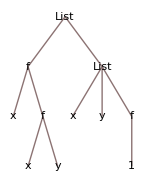

```mathematica
TreeForm[{f[x,f[x,y]],{x,y,f[1]}}]
```

Here’s a graphics expression shown in tree form:

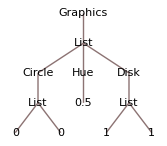

```mathematica
TreeForm[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

Because expressions ultimately have a very uniform structure, operations in the Wolfram Language operate in a very uniform way on them.

For example, any expression has parts, just like a list, and you can extract them using [[...]].

This is equivalent to {x,y,z}[[2]], which extracts the second element in a list:

```mathematica
List[x,y,z][[2]]
```

y

Extracting parts works exactly the same way for this expression:

```mathematica
f[x,y,z][[2]]
```

y

This extracts the circle from the graphics:

```mathematica
Graphics[Circle[{0,0}]][[1]]
```

Circle[{0,0}]

This goes on and extracts the coordinates of its center:

```mathematica
Graphics[Circle[{0,0}]][[1,1]]
```

{0,0}

This works exactly the same:

```mathematica
-Graphics-[[1,1]]
```

{0,0}

In f[x,y], f is called the head of the expression. x and y are called arguments. The function Head extracts the head of an expression.

The head of a list is List:

```mathematica
Head[{x,y,z}]
```

List

Every part of an expression has a head, even its atoms.

The head of an integer is Integer:

```mathematica
Head[1234]
```

Integer

The head of an approximate real number is Real:

```mathematica
Head[12.45]
```

Real

The head of a string is String:

```mathematica
Head["hello"]
```

String

Even symbols have a head: Symbol.

```mathematica
Head[x]
```

Symbol

In patterns, you can ask to match expressions with particular heads. _Integer represents any integer, _String any string and so on.

_Integer is a pattern that matches only objects with head Integer:

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

{3,4,6,7}

Named patterns can have specified heads too:

```mathematica
Cases[{99,x,y,z,101,102},n_Integer->{n,n}]
```

{{99,99},{101,101},{102,102}}

In using the Wolfram Language, most of the heads you’ll see are symbols. But there are important cases where there are more complicated heads. One such case is pure functions—where when you apply a pure function, the pure function appears as the head.

Here is the full form of a pure function (# is Slot[1]):

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

When you apply the pure function, it appears as a head:

```mathematica
Function[Power[Slot[1],2]] [1000]
```

1000000

As you become more sophisticated in Wolfram Language programming, you’ll encounter more and more examples of complicated heads. In fact, many functions that we’ve already discussed have operator forms where they appear as heads—and using them in this way leads to very powerful and elegant styles of programming.

Select appears as a head here:

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
```

{4.5,5,6,7.5,8}

Both Cases and Select appear as heads here:

```mathematica
Cases[_Integer]@Select[#>4&]@{1,2.2,3,4.5,5,6,7.5,8}
```

{5,6,8}

All the basic structural operations that we have seen for lists work exactly the same for arbitrary expressions.

Length does not care what the head of an expression is; it just counts arguments:

```mathematica
Length[f[x,y,z]]
```

3

/@ does not care about the head of an expression either; it just applies a function to the arguments:

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

Since there are lots of functions that generate lists, it’s often convenient to build up structures as lists even if eventually one needs to replace the lists with other functions.

@@ effectively replaces the head of the list with f:

```mathematica
f@@{x,y,z}
```

f[x,y,z]

This yields Plus[1,1,1,1], which then evaluates:

```mathematica
Plus@@{1,1,1,1}
```

4

This turns a list into a rule:

```mathematica
#1->#2&@@{x,y}
```

x→y

Here’s a simpler alternative, without the explicit pure function:

```mathematica
Rule@@{x,y}
```

x→y

A surprisingly common situation is to have a list of lists, and to want to replace the inner lists with some function. It’s possible to do this with @@ and /@. But @@@ provides a convenient direct way to do it.

Replace the inner lists with f:

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

Turn the inner lists into rules:

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

Here’s an example of how @@@ can help construct a graph from a list of pairs.

This generates a list of pairs of characters:

```mathematica
Partition[Characters["antidisestablishmentarianism"],2,1]
```

{{a,n},{n,t},{t,i},{i,d},{d,i},{i,s},{s,e},{e,s},{s,t},{t,a},{a,b},{b,l},{l,i},{i,s},{s,h},{h,m},{m,e},{e,n},{n,t},{t,a},{a,r},{r,i},{i,a},{a,n},{n,i},{i,s},{s,m}}

Turn this into a list of rules:

```mathematica
Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

Form a transition graph showing how letters follow each other:

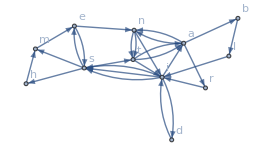

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```

Vocabulary

FullForm[expr] |   | show full internal form 
TreeForm[expr] |   | show tree structure 
Head[expr] |   | extract the head of an expression 
_head |   | match any expression with a particular head
f@@list |   | replace the head of list with f
f@@@{list_1,list_2, ...} |   | replace heads of list_1, list_2, ... with f

"8 Exercises Available" | "Get Started »"

Find the head of the output from ListPlot. »

| Expected output: |  
  | Graphics |

Use @@ to compute the result of multiplying together integers up to 100. »

| Expected output: |  
  | 93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 |

Use @@@ and Tuples to generate {f[a,a],f[a,b],f[b,a],f[b,b]}. »

| Expected output: |  
  | {f[a,a],f[a,b],f[b,a],f[b,b]} |

Make a list of tree forms for the results of 4 successive applications of #^#& starting from x. »

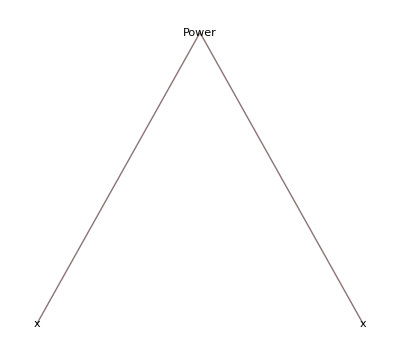
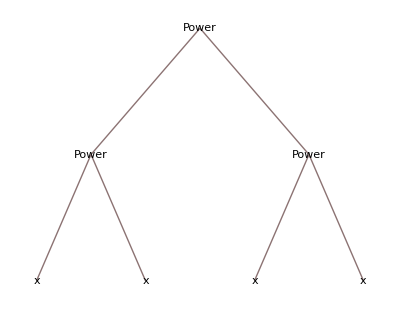
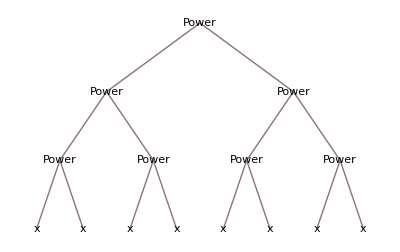
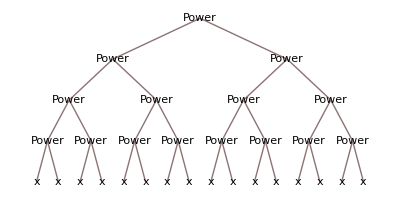
| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Find the unique cases where i^2/(j^2+1) is an integer, with i and j going up to 20. »

| Expected output: |  
  | {2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200} |

Create a graph that connects successive pairs of numbers in Table[Mod[n^2+n,100],{n,100}]. »

| Expected output: |  
  | -Graphics- |

Generate a graph showing which word can follow which in the first 200 words of the Wikipedia article on computers. »

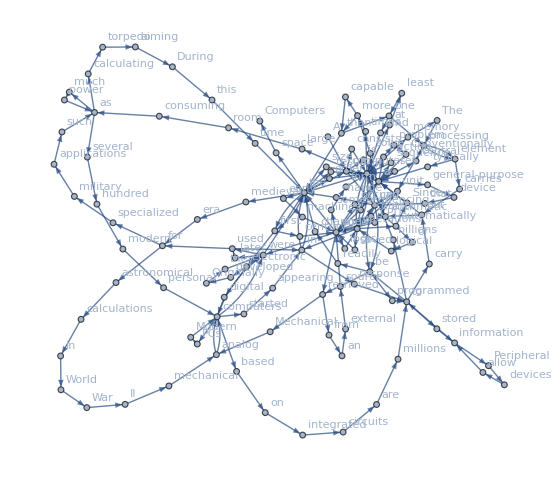
| Sample expected output: |  
  | -Graphics- |

Find a simpler form for f@@#&/@{{1,2},{7,2},{5,4}}. »

| Sample expected output: |  
  | {f[1,2],f[7,2],f[5,4]} |

Q&A

How are @@ and @@@ interpreted?

f@@expr is Apply[f,expr]. f@@@expr is Apply[f,expr,{1}]. They’re usually just read as “double at” and “triple at”.

Are all expressions in the Wolfram Language trees?

At a structural level, yes. When there are variables with values assigned (see Section 38), though, they can behave more like directed graphs. And of course one can use Graph to represent any graph as an expression in the Wolfram Language.

Tech Notes

The basic concept of symbolic languages comes directly from work in mathematical logic stretching back to the 1930s and before, but other than in the Wolfram Language it’s been very rare for it to be implemented in practice.

Wolfram Language expressions are a bit like XML expressions (and can be converted to and from them). But unlike XML expressions, Wolfram Language expressions can evaluate so that they automatically change their structure.

Things like Select[f] that are set up to be applied to expressions are called operator forms, by analogy with operators in mathematics. Using Select[f][expr] instead of Select[expr,f] is often called currying, after a logician named Haskell Curry.

Symbols like x can be used to represent algebraic variables or “unknowns”. This is central to doing many kinds of mathematics in the Wolfram Language.

LeafCount gives the total number of atoms at the leaves of an expression tree. ByteCount gives the number of bytes needed to store the expression.

More to Explore

Guide to Expressions in the Wolfram Language »